# Bistable motif: 2kinase1substrate

## The model

We consider the following reactions:

K+S→KS→K+S_p
K_p+S→K_p S→K_p+S_p
K→K_p
KS←K_p S
E+S→ES→E+S_p
E_p+S→E_p S→E_p+S_p
E→E_p
ES←E_p S
S_p→S

The species of the system are:

{S,S_p,K,K_p,KS,K_p S,E,E_p,ES,E_p S}

In total, there are 13 reations and 10 species.

## Finding the condition of multistationarity

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{13},{10}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;
A[[2]][[3]]=1;A[[2]][[2]]=1;A[[2]][[5]]=-1;
A[[3]][[1]]=-1;A[[3]][[4]]=-1;A[[3]][[6]]=1;
A[[4]][[4]]=1;A[[4]][[2]]=1;A[[4]][[6]]=-1;
A[[5]][[3]]=-1;A[[5]][[4]]=1;A[[6]][[5]]=1;A[[6]][[6]]=-1;
A[[13]][[2]]=-1;A[[13]][[1]]=1;
A[[7]][[1]]=-1;A[[7]][[7]]=-1;A[[7]][[9]]=1;
A[[8]][[7]]=1;A[[8]][[2]]=1;A[[8]][[9]]=-1;
A[[9]][[1]]=-1;A[[9]][[8]]=-1;A[[9]][[10]]=1;
A[[10]][[8]]=1;A[[10]][[2]]=1;A[[10]][[10]]=-1;
A[[11]][[7]]=-1;A[[11]][[8]]=1;
A[[12]][[9]]=1;A[[12]][[10]]=-1;
```

```mathematica
stoiM=Transpose[A]
```

{{-1,0,-1,0,0,0,-1,0,-1,0,0,0,1},{0,1,0,1,0,0,0,1,0,1,0,0,-1},{-1,1,0,0,-1,0,0,0,0,0,0,0,0},{0,0,-1,1,1,0,0,0,0,0,0,0,0},{1,-1,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,-1,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,-1,0,0},{0,0,0,0,0,0,0,0,-1,1,1,0,0},{0,0,0,0,0,0,1,-1,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,-1,0,-1,0}}

```mathematica
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 4]×Subscript[x, 6],Subscript[k, 5]×Subscript[x, 3],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 7]×Subscript[x, 1],Subscript[k, 8]×Subscript[x, 9],Subscript[k, 9]×Subscript[x, 8]*Subscript[x, 1],Subscript[k, 10]*Subscript[x, 10],Subscript[k, 11]*Subscript[x, 7],Subscript[k, 12]×Subscript[x, 10],Subscript[k, 13]*Subscript[x, 2]}
```

{k_1 x_1 x_3,k_2 x_5,k_3 x_1 x_4,k_4 x_6,k_5 x_3,k_6 x_6,k_7 x_1 x_7,k_8 x_9,k_9 x_1 x_8,k_10 x_10,k_11 x_7,k_12 x_10,k_13 x_2}

```mathematica
ssEqns=stoiM.ks
```

{k_13 x_2-k_1 x_1 x_3-k_3 x_1 x_4-k_7 x_1 x_7-k_9 x_1 x_8,-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,-k_5 x_3-k_1 x_1 x_3+k_2 x_5,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,-k_11 x_7-k_7 x_1 x_7+k_8 x_9,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,k_9 x_1 x_8-k_10 x_10-k_12 x_10}

```mathematica
mC=RowReduce[NullSpace[A]]
```

{{1,1,0,0,1,1,0,0,1,1},{0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,1,1}}

```mathematica
cons={Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2],Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 3]};
```

```mathematica
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],ssEqns[[8]],ssEqns[[9]],cons[[1]],cons[[2]],cons[[3]]}
```

{-k_13 x_2+k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10,k_5 x_3-k_3 x_1 x_4+k_4 x_6,k_1 x_1 x_3-k_2 x_5+k_6 x_6,k_3 x_1 x_4-k_4 x_6-k_6 x_6,k_11 x_7-k_9 x_1 x_8+k_10 x_10,k_7 x_1 x_7-k_8 x_9+k_12 x_10,-T_1+x_1+x_2+x_5+x_6+x_9+x_10,-T_2+x_3+x_4+x_5+x_6,-T_3+x_7+x_8+x_9+x_10}

```mathematica
sol1=Solve[{ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],cons[[2]]}==0,{Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

{{x_3→(k_2 k_3 k_6 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_4→(k_2 k_5 (k_4+k_6) T_2)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_5→(k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2),x_6→(k_2 k_3 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)}}

```mathematica
sol2=Solve[{ssEqns[[8]],ssEqns[[9]],ssEqns[[10]],cons[[3]]}==0,{Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10]}]
```

{{x_7→(k_8 k_9 k_12 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_8→(k_8 k_11 (k_10+k_12) T_3)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_9→(k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2),x_10→(k_8 k_9 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)}}

```mathematica
sol3=Subscript[x, 2]/.Solve[{ssEqns[[2]]==0},{Subscript[x, 2]}]
```

{(k_2 x_5+k_4 x_6+k_8 x_9+k_10 x_10)/k_13}

```mathematica
sol4=Solve[{Subscript[x, 2]==sol3[[1]]}/.Join[sol1[[1]],sol2[[1]]],{Subscript[x, 2]}]
```

{{x_2→1/k_13((k_2 k_3 k_4 k_5 T_2 x_1)/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_2 k_3 T_2 (k_5 k_6 x_1+k_1 k_6 x_1^2))/(k_2 k_4 k_5+k_2 k_5 k_6+k_2 k_3 k_5 x_1+k_2 k_3 k_6 x_1+k_3 k_5 k_6 x_1+k_1 k_3 k_6 x_1^2)+(k_8 k_9 k_10 k_11 T_3 x_1)/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2)+(k_8 k_9 T_3 (k_11 k_12 x_1+k_7 k_12 x_1^2))/(k_8 k_10 k_11+k_8 k_11 k_12+k_8 k_9 k_11 x_1+k_8 k_9 k_12 x_1+k_9 k_11 k_12 x_1+k_7 k_9 k_12 x_1^2))}}

```mathematica
term=FullSimplify[Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 9]+Subscript[x, 10]-Subscript[T, 1]/.Join[sol1[[1]],sol2[[1]],sol4[[1]]]]
```

-T_1+(x_1 ((k_3 T_2 (k_5 (k_6 k_13+k_2 (k_4+k_6+k_13))+k_1 k_6 (k_2+k_13) x_1))/(k_3 k_6 x_1 (k_5+k_1 x_1)+k_2 (k_5 (k_4+k_6)+k_3 (k_5+k_6) x_1))+(k_9 k_12 k_13 (T_3+x_1) (k_11+k_7 x_1)+k_8 (k_11 ((k_10+k_12) k_13+k_9 (k_10+k_12+k_13) T_3)+k_9 ((k_11+k_12) k_13+k_7 k_12 T_3) x_1))/(k_9 k_12 x_1 (k_11+k_7 x_1)+k_8 (k_11 (k_10+k_12)+k_9 (k_11+k_12) x_1))))/k_13

```mathematica
polynomial=Collect[Numerator[Together[term]],Subscript[x, 1]]
```

-k_2 k_4 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_11 k_12 k_13 T_1+(k_2 k_4 k_5 k_8 k_10 k_11 k_13+k_2 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_11 k_12 k_13+k_2 k_5 k_6 k_8 k_11 k_12 k_13-k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_10 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_10 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_4 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_4 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1+(k_2 k_4 k_5 k_8 k_9 k_11 k_13+k_2 k_5 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_8 k_10 k_11 k_13+k_2 k_3 k_6 k_8 k_10 k_11 k_13+k_3 k_5 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_8 k_9 k_12 k_13+k_2 k_5 k_6 k_8 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_11 k_12 k_13+k_2 k_3 k_6 k_8 k_11 k_12 k_13+k_3 k_5 k_6 k_8 k_11 k_12 k_13+k_2 k_4 k_5 k_9 k_11 k_12 k_13+k_2 k_5 k_6 k_9 k_11 k_12 k_13-k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_1-k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_1-k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_1-k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_1-k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_1-k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_1+k_2 k_3 k_4 k_5 k_8 k_9 k_11 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_11 T_2+k_1 k_2 k_3 k_6 k_8 k_10 k_11 T_2+k_2 k_3 k_4 k_5 k_8 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_11 k_12 T_2+k_2 k_3 k_4 k_5 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_6 k_9 k_11 k_12 T_2+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_2+k_1 k_3 k_6 k_8 k_10 k_11 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_2+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_2+k_2 k_3 k_5 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_3 k_5 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_4 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_12 T_3+k_2 k_3 k_5 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_3 k_5 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_4 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_5 k_9 k_11 k_12 k_13 T_3+k_2 k_3 k_6 k_9 k_11 k_12 k_13 T_3+k_3 k_5 k_6 k_9 k_11 k_12 k_13 T_3) x_1^2+(k_2 k_3 k_5 k_8 k_9 k_11 k_13+k_2 k_3 k_6 k_8 k_9 k_11 k_13+k_3 k_5 k_6 k_8 k_9 k_11 k_13+k_1 k_3 k_6 k_8 k_10 k_11 k_13+k_2 k_4 k_5 k_7 k_9 k_12 k_13+k_2 k_5 k_6 k_7 k_9 k_12 k_13+k_2 k_3 k_5 k_8 k_9 k_12 k_13+k_2 k_3 k_6 k_8 k_9 k_12 k_13+k_3 k_5 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_11 k_12 k_13+k_2 k_3 k_5 k_9 k_11 k_12 k_13+k_2 k_3 k_6 k_9 k_11 k_12 k_13+k_3 k_5 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_1-k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_1-k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_1-k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_1-k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_8 k_9 k_11 T_2+k_2 k_3 k_4 k_5 k_7 k_9 k_12 T_2+k_2 k_3 k_5 k_6 k_7 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_8 k_9 k_12 T_2+k_1 k_2 k_3 k_6 k_9 k_11 k_12 T_2+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_2+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_2+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_2+k_1 k_3 k_6 k_8 k_9 k_10 k_11 T_3+k_2 k_3 k_5 k_7 k_8 k_9 k_12 T_3+k_2 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_3 k_5 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_12 T_3+k_1 k_3 k_6 k_8 k_9 k_11 k_13 T_3+k_2 k_3 k_5 k_7 k_9 k_12 k_13 T_3+k_2 k_3 k_6 k_7 k_9 k_12 k_13 T_3+k_3 k_5 k_6 k_7 k_9 k_12 k_13 T_3+k_1 k_3 k_6 k_9 k_11 k_12 k_13 T_3) x_1^3+(k_1 k_3 k_6 k_8 k_9 k_11 k_13+k_2 k_3 k_5 k_7 k_9 k_12 k_13+k_2 k_3 k_6 k_7 k_9 k_12 k_13+k_3 k_5 k_6 k_7 k_9 k_12 k_13+k_1 k_3 k_6 k_8 k_9 k_12 k_13+k_1 k_3 k_6 k_9 k_11 k_12 k_13-k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_1+k_1 k_2 k_3 k_6 k_7 k_9 k_12 T_2+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_2+k_1 k_3 k_6 k_7 k_8 k_9 k_12 T_3+k_1 k_3 k_6 k_7 k_9 k_12 k_13 T_3) x_1^4+k_1 k_3 k_6 k_7 k_9 k_12 k_13 x_1^5

This is a degree 5 polynomial which presumably admits 5 positive real roots. Any real root of this polynomial leads to a steady state for the fixed rate constants and total amounts. The values of the other variables at steady states are found by plugging the value of x1 (the root of the polynomial) into the expressions in sol1, sol2, and sol3 above.

A necessary condition for 5 positive roots is that the signs of the coefficient of the polynomial (in x1) alternate.
This is a pre-check when you do the sampling: you need to impose the coefficient of x1^4 to be  negative , the coefficient of x1^3 to be positive, the coefficient of x1^2 to be  negative and the coefficient of x1 to be positive. The coefficients of x1^5 and the independent term always have the right sign.

## Sampling the parameters to make the term has 5 roots

```mathematica
ClearAll["Global`*"];
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^3+(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[x, 1]^5;
```

#### Coeffs

```mathematica
coeff1=Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3];
coeff2=(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff3=(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
coeff4=(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]);
```

#### Sampling

```mathematica
ss2ParSets={};
ss2PolSets={};
ss2SolSets={};
ss3ParSets={};
ss3PolSets={};
ss3SolSets={};
ss4ParSets={};
ss4PolSets={};
ss4SolSets={};
ss5ParSets={};
ss5PolSets={};
ss5SolSets={};
biCount=0;
multiCount=0;
termCount=0;
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{Log[0.001],Log[1000.]},13]];
tots=Exp[RandomReal[{Log[0.001],Log[1000.]},3]];
subs={Subscript[k, 1]->pars[[1]],Subscript[k, 2]->pars[[2]],Subscript[k, 3]->pars[[3]],Subscript[k, 4]->pars[[4]],Subscript[k, 5]->pars[[5]],Subscript[k, 6]->pars[[6]],Subscript[k, 7]->pars[[7]],Subscript[k, 8]->pars[[8]],Subscript[k, 9]->pars[[9]],Subscript[k, 10]->pars[[10]],Subscript[k, 11]->pars[[11]],Subscript[k, 12]->pars[[12]],Subscript[k, 13]->pars[[13]],Subscript[T, 1]->tots[[1]],Subscript[T, 2]->tots[[2]],Subscript[T, 3]->tots[[3]]};
(*term4=coeff4/.subs;term3=coeff3/.subs;term2=coeff2/.subs;term1=coeff1/.subs;
If[term4<0&&term3>0&&term2<0&&term1>0,{*)
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
(*termCount++;*)
Switch[Length[Flatten[solution]],2,{
AppendTo[ss2ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss2PolSets,pol/.subs];
AppendTo[ss2SolSets,Flatten[solution]];
biCount++;},3,{
AppendTo[ss3ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss3PolSets,pol/.subs];
AppendTo[ss3SolSets,Flatten[solution]];
multiCount++;},4,{
AppendTo[ss4ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss4PolSets,pol/.subs];
AppendTo[ss4SolSets,Flatten[solution]];
multiCount++;},5,{
AppendTo[ss5ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss5PolSets,pol/.subs];
AppendTo[ss5SolSets,Flatten[solution]];
multiCount++;}
];
(*}];*)
},{i,5000000}];
]
```

{15675.3,Null}

#### Check results

```mathematica
Length[ss2ParSets]
```

40267

```mathematica
Length[ss3ParSets]
```

6513

```mathematica
Length[ss4ParSets]
```

135

```mathematica
Length[ss5ParSets]
```

4

#### Save all sampling data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["2kinase_ss5ParSets.csv",ss5ParSets];
```

```mathematica
Export["2kinase_ss5SolSets.csv",ss5SolSets];
```

```mathematica
Export["2kinase_ss5PolSets.csv",ss5PolSets];
```

```mathematica
Export["2kinase_ss4ParSets.csv",ss4ParSets];
Export["2kinase_ss4SolSets.csv",ss4SolSets];
Export["2kinase_ss4PolSets.csv",ss4PolSets];

Export["2kinase_ss3ParSets.csv",ss3ParSets];
Export["2kinase_ss3SolSets.csv",ss3SolSets];
Export["2kinase_ss3PolSets.csv",ss3PolSets];

Export["2kinase_ss2ParSets.csv",ss2ParSets];
Export["2kinase_ss2SolSets.csv",ss2SolSets];
Export["2kinase_ss2PolSets.csv",ss2PolSets];
```

### SS5

#### Show the parameters

```mathematica
InputForm[ss5ParSets]
```

{{30.26907055950005, 0.015345031904046718, 379.2818135708148, 3.8082251354658188, 0.0036687528444848427, 
 0.13296589686376084, 310.1595399836181, 0.021043418057000815, 0.016491372377285016, 39.76104156980563, 9.061356696657525, 
 0.023576257909081366, 0.0023689836151906487, 845.7868156657265, 57.56286728182886, 16.45292963069698}, {12.791536262377333, 
 0.0034898324955981988, 124.48490665956912, 14.364956625123318, 1.8820643829200225, 0.06207039508084975, 5.36634369662495, 
 0.1395233965784267, 6.127307127467282, 348.2943196285812, 0.6139560154556575, 0.004203521315153397, 0.006595294405600259, 
 431.8992457693107, 12.136890753339557, 0.18502617556413403}, {5.879137085516735, 0.0033751979024755916, 2.107719796978838, 
 500.69023689470674, 0.037972916416413455, 48.025982227857675, 67.40947817881231, 0.004277486460006026, 0.16410793866624665, 
 30.195763275878235, 0.4278526927277934, 0.002727157259805876, 0.0015127395140503617, 829.7331212580159, 110.97744997193716, 
 25.07248294701992}, {0.03863067640002412, 0.06964020400731227, 12.893107874913023, 717.0141199745967, 0.016845994678178475, 
 0.001941863314613148, 0.515261967967496, 0.0011924697492939357, 58.62046075778042, 242.79254583735883, 
 0.0018562783780476306, 4.143110610314261, 0.0034828788856501665, 980.5678137212656, 0.02294111016031769, 
 200.56979547299036}}

```mathematica
InputForm[ss5SolSets]
```

{{0.0001673179574018385, 0.0017701734788143613, 4.211495208850604, 28.136233827022362, 220.35377804688864}, 
 {0.0026993292596905116, 0.5143459784462802, 1.8447433928056391, 126.15341072811653, 276.6322493206081}, 
 {0.011201423386435755, 0.024705675213822165, 0.13170436103981822, 13.63860745022466, 361.34661097799966}, 
 {0.00045859801424694336, 0.013160505343201727, 11.37445257762346, 92.04118330552284, 589.5323347053119}}

```mathematica
ss5SolSets
```

{{0.000167318,0.00177017,4.2115,28.1362,220.354},{0.00269933,0.514346,1.84474,126.153,276.632},{0.0112014,0.0247057,0.131704,13.6386,361.347},{0.000458598,0.0131605,11.3745,92.0412,589.532}}

```mathematica
InputForm[ss5ParSets[[3]]]
```

{5.879137085516735, 0.0033751979024755916, 2.107719796978838, 500.69023689470674, 0.037972916416413455, 
48.025982227857675, 67.40947817881231, 0.004277486460006026, 0.16410793866624665, 30.195763275878235, 
0.4278526927277934, 0.002727157259805876, 0.0015127395140503617, 829.7331212580159, 110.97744997193716, 
25.07248294701992}

#### Get the parameters

```mathematica
ss5Par3={5.879137085516735,0.0033751979024755916,2.107719796978838,500.69023689470674,0.037972916416413455,48.025982227857675,67.40947817881231,0.004277486460006026,0.16410793866624665,30.195763275878235,0.4278526927277934,0.002727157259805876,0.0015127395140503617,829.7331212580159,110.97744997193716,25.07248294701992}
```

{5.87914,0.0033752,2.10772,500.69,0.0379729,48.026,67.4095,0.00427749,0.164108,30.1958,0.427853,0.00272716,0.00151274,829.733,110.977,25.0725}

```mathematica
parSet={Subscript[k, 1]->ss5Par3[[1]],Subscript[k, 2]->ss5Par3[[2]],Subscript[k, 3]->ss5Par3[[3]],Subscript[k, 4]->ss5Par3[[4]],Subscript[k, 5]->ss5Par3[[5]],Subscript[k, 6]->ss5Par3[[6]],Subscript[k, 7]->ss5Par3[[7]],Subscript[k, 8]->ss5Par3[[8]],Subscript[k, 9]->ss5Par3[[9]],Subscript[k, 10]->ss5Par3[[10]],Subscript[k, 11]->ss5Par3[[11]],Subscript[k, 12]->ss5Par3[[12]],Subscript[k, 13]->ss5Par3[[13]],Subscript[T, 1]->ss5Par3[[14]](*,Subscript[T, 2]->ss5Par3[[15]],Subscript[T, 3]->ss5Par3[[16]]*)};
```

```mathematica
polx1=pol==0/.parSet
```

-0.00487856+(-0.290402+0.00851361 T_2+0.000637903 T_3) x_1+(-41.2881+0.160843 T_2+0.0379793 T_3) x_1^2+(-0.477551+0.0060836 T_2+5.39877 T_3) x_1^3+(-22.5348+0.0877585 T_2+0.103958 T_3) x_1^4+0.0271599 x_1^5==0

#### ParSet[[3]]: Varying T_2

```mathematica
oneDT2=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2,Subscript[T, 3]->25.07248294701992},{Subscript[x, 1]}],{T2,0,300,1}];
```

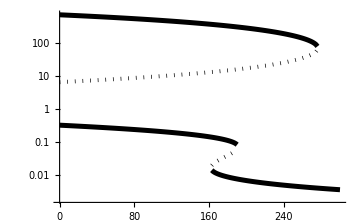

```mathematica
ListLogPlot[(*Join[{Range[0,200,0.1]},*)Transpose[oneDT2[[1;;200]]](*]*),Joined->True,ImageSize->Medium,DataRange->{0,300},PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]}]
```

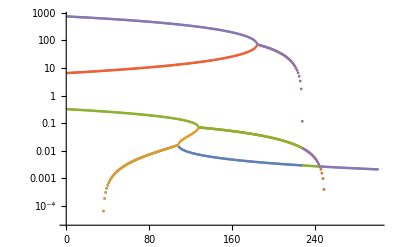

```mathematica
ListLogPlot[Transpose[Re[oneDT2]]]
```

#### ParSet[[3]]: Varying T_3

```mathematica
oneDT3=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->110.97744997193716,Subscript[T, 3]->T3(*25.07248294701992*)},{Subscript[x, 1]}],{T3,0,80,0.1}];
```

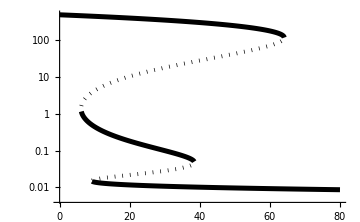

```mathematica
ListLogPlot[(*Join[{Range[0,200,0.1]},*)Transpose[oneDT3(*[[1;;100]]*)](*]*),DataRange->{0,80},Joined->True,ImageSize->Medium,PlotStyle->{{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]},{Black,Dotted,Thickness[0.008]},{Black,Thickness[0.01]}},(*PlotRange->{{0,200},{0.001,1000}},*)LabelStyle->{14,GrayLevel[0]}]
```

#### ParSet[[3]]: Varying both T_2 and T_3

```mathematica
twoD=Table[Subscript[x, 1]/.NSolve[{polx1}/.{Subscript[T, 2]->T2(*110.97744997193716*),Subscript[T, 3]->T3(*25.07248294701992*)},{Subscript[x, 1]}],{T2,0,280,2.8},{T3,0,160,1.6}];
```

```mathematica
normal3D=ListPointPlot3D[Log10[Transpose[twoD,{2,3,1}]],DataRange->{{0,280},{0,160}},PlotStyle->PointSize[Medium],ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ViewPoint->{-1.9678567233048574,-2.120404270561833,-1.7553989990674568},ViewVertical->{-0.06442955334612624,-0.058712697461734124,-2.4904839537381904}]
```

-Graphics3D-

```mathematica
optsNormal3D=-Graphics3D-//Options
```

{Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,0.4},FaceGridsStyle→Automatic,ImageSize→{396.9,288.539},LabelStyle→{18,GrayLevel[0]},PlotRange→{{0.,280.},{0.,160.},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{-1.96786,-2.1204,-1.7554},ViewVertical→{-0.0644296,-0.0587127,-2.49048}}

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]},PlotStyle->PointSize[Medium],PlotLegends->Automatic,ViewPoint->{-1.9678567233048574,-2.120404270561833,-1.7553989990674568},ViewVertical->{-0.06442955334612624,-0.058712697461734124,-2.4904839537381904},ImageSize->Large]]
```

-Graphics-

ContourPlot3D:

```mathematica
logTransTwoD=Log10[Transpose[twoD,{2,3,1}]];dim=Dimensions[logTransTwoD];t2=Range[0,280,2.8];t3=Range[0,160,1.6];
```

```mathematica
nestedCoords=Table[{t2[[k]],t3[[j]],logTransTwoD[[i]][[j]][[k]]},{i,1,dim[[1]]},{j,1,dim[[2]]},{k,1,dim[[3]]}];
```

```mathematica
coords=Table[Flatten[nestedCoords[[i]],1],{i,1,Length[nestedCoords]}];
```

```mathematica
(*Cannot use contour plot, shame*)
small3D=ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]}(*,PlotStyle->PointSize[Small]*),ImageSize->Large]
```

-Graphics3D-

```mathematica
optsSmall3D=-Graphics3D-//Options
```

{Axes→True,AxesLabel→{None,None,None},BoxRatios→{1,1,0.4},FaceGridsStyle→Automatic,ImageSize→{362.874,307.339},LabelStyle→{18,GrayLevel[0]},PlotRange→{{0.,280.},{0.,160.},Automatic},PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]},{Automatic,Automatic}},Ticks→{Automatic,Automatic,Automatic},ViewPoint→{1.69265,1.82147,2.29504},ViewVertical→{-0.0963563,-0.0639817,2.48322}}

```mathematica
Rasterize[ListPointPlot3D[coords,ColorFunction->"Rainbow",LabelStyle->{18,GrayLevel[0]}(*,PlotStyle->PointSize[Small]*),PlotLegends->Automatic,ViewPoint->{10, 10, 10},ImageSize->Large]]
```

-Graphics-

## Using repetitive parameters from 1 kinase 1 substrate system

```mathematica
ClearAll["Global`*"];
```

```mathematica
pol=-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]+(Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^2+(Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 10] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 10] Subscript[k, 11] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^3+(Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 11] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 5] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 3] Subscript[k, 5] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 11] Subscript[k, 12] Subscript[k, 13]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 1]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 2]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 8] Subscript[k, 9] Subscript[k, 12] Subscript[T, 3]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[T, 3]) Subscript[x, 1]^4+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 7] Subscript[k, 9] Subscript[k, 12] Subscript[k, 13] Subscript[x, 1]^5;
```

```mathematica
par13={Subscript[k, 1]->7.0209900641524134,Subscript[k, 2]->0.001316524683661764,Subscript[k, 3]->905.3281836995496,Subscript[k, 4]->669.9638136659813,Subscript[k, 5]->0.23999129836112074,Subscript[k, 6]->0.12556292708100278,Subscript[k, 13]->0.0016709212401803638,Subscript[T, 1]-> 0.8910420201362843,Subscript[T, 2]->0.0012885286945288495};
```

```mathematica
parTest={Subscript[k, 1]->7.0209900641524134,Subscript[k, 2]->0.001316524683661764,Subscript[k, 3]->905.3281836995496,Subscript[k, 4]->669.9638136659813,Subscript[k, 5]->0.23999129836112074,Subscript[k, 6]->0.12556292708100278,Subscript[k, 7]->7.0209900641524134,Subscript[k, 8]->0.001316524683661764,Subscript[k, 9]->905.3281836995496,Subscript[k, 10]->669.9638136659813,Subscript[k, 11]->0.23999129836112074,Subscript[k, 12]->0.12556292708100278,Subscript[k, 13]->0.0016709212401803638,Subscript[T, 1]-> 0.8910420201362843,Subscript[T, 2]->0.0012885286945288495,Subscript[T, 3]->0.0012885286945288495};
```

```mathematica
Solve[pol==0/.parTest,Subscript[x, 1]]
```

{{x_1→-0.0233835},{x_1→-0.0113444},{x_1→0.000696815},{x_1→0.425505-0.397691 ⅈ},{x_1→0.425505+0.397691 ⅈ}}

```mathematica
ss5ParSets={};
ss5PolSets={};
ss5SolSets={};
Timing[
Do[{
(*pars=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],13]]*1000;
tots=Exp[-RandomVariate[ExponentialDistribution[Log[2]/(-Log[0.001])],3]]*1000;*)
pars=Exp[RandomReal[{Log[0.000001],Log[1000000.]},6]];
tots=Exp[RandomReal[{Log[0.0001],Log[10000.]},1]];
subs=Flatten[{par13,Subscript[k, 7]->pars[[1]],Subscript[k, 8]->pars[[2]],Subscript[k, 9]->pars[[3]],Subscript[k, 10]->pars[[4]],Subscript[k, 11]->pars[[5]],Subscript[k, 12]->pars[[6]],Subscript[T, 3]->tots[[1]]}];
solution=Select[DeleteDuplicates[Re[Subscript[x, 1]/.NSolve[{pol==0}/.subs,Subscript[x, 1]]]],Positive];
If[Length[Flatten[solution]]==5,{
AppendTo[ss5ParSets,Flatten[Join[pars,tots]]];
AppendTo[ss5PolSets,pol/.subs];
AppendTo[ss5SolSets,Flatten[solution]];
}
];
},{i,1000000}];
]
```

{2827.48,Null}

```mathematica
Length[ss5ParSets]
```

165

#### Save all sampling data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["2kinase_ss5ParSets2.csv",ss5ParSets];
Export["2kinase_ss5SolSets2.csv",ss5SolSets];
Export["2kinase_ss5PolSets2.csv",ss5PolSets];
```

```mathematica
InputForm[ss5ParSets]
```

{{5084.132603487649, 2.711981884531638*^-6, 107552.92737082136, 16697.042155624637, 8.551598118853089*^-6, 
 0.00004266257468708378, 0.01782945264393229}, {149.1301218799367, 0.0007324776293031722, 789053.7262158421, 
 8.74607258604299, 0.00025900134808836577, 0.00002707275249086464, 0.0009277807568589512}, {2978.6355559066214, 
 0.0001501028008663726, 7518.053195652338, 88663.14485374973, 1.3718504273243037*^-6, 0.00004330012707113969, 
 0.003340681698787888}, {24857.01399594304, 0.00010386084849916813, 325055.45213864587, 3.8248426373920275, 
 0.023996224085886732, 0.00006972883962157908, 0.013551058046553332}, {0.48710310090901227, 0.00001920007368885381, 
 14306.04217604721, 720.8060337033701, 0.00001432732893697504, 0.01506620499752257, 0.01852442029371901}, 
 {2520.2684234727944, 0.026265025070615747, 444941.9567258774, 456872.23476647766, 5.369551489731419*^-6, 0.9965662728919342, 
 0.0019360595872804792}, {18723.676177530742, 0.026425272373842686, 119640.61944960462, 410077.2744534494, 
 0.0001711625905675158, 0.8710832971103378, 0.0010455739317485366}, {7339.714077420352, 0.0001287461615530396, 
 559.9914474962764, 5764.65650919472, 0.00021006597050580146, 0.002699664800521245, 0.04489402250619763}, 
 {484942.15697902814, 4.330107398990631*^-6, 49356.840596225724, 5.753125796938967, 3.120917773594966, 9.48324045746867*^-6, 
 0.01542566243930293}, {1039.7217780906824, 0.0006527554773109599, 86540.92710537855, 0.19087307913846224, 
 0.00863074589403079, 0.00022057510228737918, 0.039940831754314864}, {9.54023213158876, 2.8784185479273997*^-6, 
 222875.61567011365, 210463.81664518308, 0.00002407137713421249, 0.06860959665975148, 0.014515631622444396}, 
 {553.078421355306, 0.000037048005199947876, 40452.26690938248, 740.5769824730586, 0.021240132733123807, 0.05823167659500112, 
 0.008812785350789854}, {14047.488973278256, 0.004844582410013452, 948533.7654683994, 2025.488131287726, 
 0.000010573048547481494, 0.0006660275993159442, 0.0018231401976922354}, {56.96068229511391, 0.00016253252774801614, 
 11053.648167031834, 525.3067697889618, 0.00024793873633624443, 0.016799404181039253, 0.007353124774989458}, 
 {398.58839321165647, 0.00001016968063889541, 545797.9214676654, 7479.72218823651, 1.9321442245627916*^-6, 
 0.000032557422461345976, 0.008706167393625674}, {560.5540631977833, 0.0014542431779376453, 24029.358169912848, 
 0.4608205776663559, 0.0001431856016404744, 0.000020561544430302468, 0.027633144501863258}, {16829.214331717336, 
 0.00003677743487174563, 788320.1927538998, 9.203025747873003, 0.19629786449490236, 6.836826552324129*^-6, 
 0.0006785730301505644}, {94896.18581458674, 0.001508272809673922, 873590.8594446275, 885394.3342463099, 
 0.0017491588431090385, 10.51153271526236, 0.00830858510135611}, {188966.78432134097, 3.4281350720526355*^-6, 
 740342.1432592846, 38936.624924986034, 5.96489226108305, 0.13661175497572997, 0.0032279214560014375}, {93.00489720452083, 
 0.0012540565725768548, 258052.6787337258, 27.73175754728672, 0.010199633571563302, 0.14871534499931513, 
 0.01791441979706251}, {34163.9850693214, 0.0010271755325959042, 307941.51218568574, 32152.31231586961, 
 0.0001727325433382279, 0.4504332258210616, 0.017716604544391487}, {3.5217823774016663, 0.001036230568311457, 
 606633.2086752304, 8192.354109621512, 0.0006878653897900678, 1.9923841722877609, 0.0010496774213216511}, 
 {53277.606794947125, 0.0003622883997389867, 601157.933803973, 15.407296796951082, 0.0186833349598088, 0.007640129806363571, 
 0.013013037332236745}, {154057.31412668922, 1.8303524611595426*^-6, 763109.0027192909, 272901.85397180426, 
 0.0018035791920044811, 0.06231110632751754, 0.04012979464450029}, {6560.843675324626, 0.008309556144036315, 
 121455.4376770339, 50062.23288999415, 0.0022437821243884667, 8.465587371057532, 0.003591569749226856}, {152.7250815403988, 
 2.828980706600394*^-6, 357979.4486258778, 67.45786362536516, 0.019435614005797623, 0.0022616725820785773, 
 0.02515860570837519}, {20.853938206900587, 0.0013320674444759527, 5794.456472992527, 1.6118610848232087, 
 0.0007800498879253592, 0.0006943991391843705, 0.005416759828026327}, {272508.2777574023, 0.0002117907525295715, 
 806682.911431697, 1669.4828306184083, 0.029752621444825343, 0.0730956349646457, 0.008527390555519513}, {804844.5478738801, 
 0.0004695281856804328, 657480.1093351912, 144694.73461825016, 0.001410065109115883, 0.07268491749684604, 
 0.04707312476410212}, {453.2370194169456, 0.00009695884949905071, 710195.8296279545, 28654.567947745083, 
 1.998893327778995*^-6, 0.05714190792497223, 0.023530328027484854}, {64.59768670303467, 1.4100307011055426*^-6, 
 12557.921845675544, 2057.749447443313, 8.882681103895774*^-6, 0.000138710010740108, 0.03184099882158815}, {408.958181421693, 
 0.0017901473642583906, 556379.0870854915, 179.33266881318758, 0.0009166892696242505, 0.00028995884293565627, 
 0.00019946122031693902}, {47.95378747373909, 1.2015454035808892*^-6, 3347.5971828647585, 172813.46612483085, 
 0.00690974975414426, 0.858767231242459, 0.014295242147029595}, {208464.40795119738, 0.0011883322045090534, 66913.8787480933, 
 7.400939283364553, 0.3506440009736386, 0.005634860703792091, 0.01831966456605555}, {149.52147004434104, 
 0.0006202105338128222, 366230.0440860686, 27.337442568470227, 1.649462763711288*^-6, 6.3707899254192625*^-6, 
 0.0015776789339735607}, {25000.347112349576, 8.395002032063511*^-6, 904645.1148534355, 84.74183695376537, 
 0.03166074439790012, 0.00004722041623888913, 0.0014767284191472229}, {56.183986290227445, 6.931763240755904*^-6, 
 56951.709692872166, 10822.670376358306, 0.00008934483088849774, 0.000438126758247441, 0.0011995751397953773}, 
 {1.529003679196492, 4.215813645141985*^-6, 157366.81823205794, 2611.369039357483, 0.000011602064537910997, 
 0.001761424521533169, 0.0021444057585483585}, {903.6760953011883, 0.00001584757678426549, 11965.655366022904, 
 35.159223967906996, 0.006613280738761634, 0.0005324171486462934, 0.048269206972054404}, {61.147944828139586, 
 0.012102148350330121, 156323.6990842247, 200.94870833001121, 0.00042854810783625447, 0.03266896990110168, 
 0.0009020876123525314}, {434680.63910972525, 0.000030952537175420964, 30297.696399745135, 30.916570487235283, 
 0.006800219142103579, 0.0000145337884443507, 0.017331791077731196}, {310526.42024803715, 0.000011153179404179761, 
 5864.067357365266, 2576.6108312443307, 0.023808027518162033, 0.0002542357460475019, 0.021629470868995075}, 
 {68.80945133092685, 0.00022239419760893307, 250754.93209717266, 1079.253931764149, 0.0063614503832507855, 2.594254797804036, 
 0.019181158779868212}, {38333.17489583218, 0.00008245529541996498, 216048.98098803178, 11673.553740717405, 
 0.043112665065193366, 0.6176515449879716, 0.029065233240781103}, {121811.81749440636, 0.00022814381856967462, 
 3876.970268075204, 3768.263797064719, 1.2417693211767602, 0.6556109201617726, 0.016784829398604695}, {1459.8230659636724, 
 0.00327805919887081, 226986.6892837152, 1228.064529799086, 0.0002442323947289142, 0.004695885057296635, 
 0.0028574006504228254}, {87912.17907188322, 0.01133087459494362, 118422.36317183528, 4.739156498520339, 
 0.002843841330947033, 8.082956025998299*^-6, 0.000906106964486761}, {94.12557029825128, 0.000024878716903866774, 
 553841.8317346419, 3377.754847388467, 1.1490898142526566*^-6, 0.0006504734169028996, 0.005980930408541921}, 
 {930.3896410859702, 8.469433182420083*^-6, 241552.97257814195, 87370.10230332511, 0.00020106629444454344, 
 0.0033063076096633854, 0.0014985489390523373}, {12705.165354149693, 0.0024740403945021122, 21338.808457065217, 
 57.601680813580764, 0.0016855106473832745, 0.00015884355483476923, 0.0018475367938269574}, {429365.4241485824, 
 1.306888657702278*^-6, 485185.6209852193, 29.014238220933134, 22.01235300606352, 7.936515832595745*^-6, 
 0.001773636054857404}, {294267.4704965141, 0.0015214813861356476, 36431.833630252775, 274408.5916651982, 
 0.01560525035983681, 4.899688099826476, 0.0147294897801488}, {3457.573546127073, 0.0012968315145925778, 169424.54118163793, 
 44866.107108935204, 0.0000225390913890684, 0.23231862209109883, 0.035607383808171945}, {187763.91801606983, 
 0.00006507886213106182, 937556.9223139676, 15.12381346432714, 0.0018436364417710337, 0.000012356070321489742, 
 0.028795261896736656}, {143.83842713930818, 0.0015817507409266103, 83684.86925929891, 393266.51043963636, 
 0.00012101761311434247, 6.852003401900922, 0.002816457615509676}, {209.21654800125594, 0.00005454065809227546, 
 27348.611531831462, 0.698939846545975, 0.00036415762475037615, 1.6054020186828555*^-6, 0.010007081070897329}, 
 {0.2851455901132889, 1.833547140465941*^-6, 769803.2933631066, 2312.6068541699683, 3.883237779238236*^-6, 
 0.0005866794176705812, 0.0006709126369636109}, {12211.86965805184, 0.0000929987467222192, 9840.896344445317, 
 72058.41422667299, 0.0002661684999723728, 0.06630133107610381, 0.020927090211114628}, {160710.09053436937, 
 0.000418087830213421, 64141.129570260346, 646.0984171416114, 0.08098642817723836, 0.018714084837964422, 
 0.02808998581488231}, {80.31202535877233, 3.3356243075913997*^-6, 990064.2952662162, 12.46491771430658, 
 0.000057802999013989324, 0.00006274928986247696, 0.023560027964774473}, {87182.36627731261, 0.0014405406817160633, 
 708739.4016084435, 68029.43388942842, 0.00004120881931185177, 0.00008922423005520995, 0.00045443389296201614}, 
 {600.3497464879096, 0.0011405841895592364, 433297.7128084462, 4439.112844276063, 5.264291312485756*^-6, 0.03481532629620398, 
 0.02195178989928699}, {30054.397714862243, 1.918566241381955*^-6, 212194.00450288548, 4538.603373425474, 
 0.00009344006165464236, 8.745540508757925*^-6, 0.005038965953164718}, {602406.8262493446, 0.0006383431864405983, 
 959526.4551186672, 1853.822598975902, 161.14097641564769, 0.3171506116756835, 0.0004979201457311348}, {2.828228129514091, 
 4.71579148579763*^-6, 149380.2762907704, 22829.1146060505, 1.621788790768783*^-6, 0.005511172494064487, 
 0.01269092663902144}, {227426.40307934722, 0.0002511893979217687, 226772.88663533758, 3466.4103546058764, 
 1.693145246537203*^-6, 0.00001186005119331476, 0.025802533848441965}, {1495.2219819334584, 0.0023910265569090363, 
 486913.9268260688, 328193.94501287764, 0.00422598595280734, 2919.845678192186, 0.0248618429913442}, {72111.52802889727, 
 0.005122655172312281, 491064.8240696747, 565337.2969534328, 0.0001507198282725993, 0.22071389699940266, 
 0.002504706119681455}, {173.4452027531118, 1.0106319212769285*^-6, 799264.3212247767, 145.56349110428303, 
 0.0010987915995424587, 3.5987191982085682*^-6, 0.0008766626084639542}, {21490.388012976484, 0.0001777857326188665, 
 321663.50373172737, 65.46729277851423, 0.0011059353089043786, 6.431182670383124*^-6, 0.0016863516364909758}, 
 {120729.0179559767, 0.00004255718526849254, 515099.49846984545, 79198.15904432359, 0.0632497313615726, 6.6592590326609375, 
 0.04352043537020368}, {70230.82275646845, 0.00041136106541027605, 3464.215132020051, 3.070392470696892, 
 0.015836158883496286, 0.000027150881453355184, 0.04346844693049497}, {24792.896184502973, 0.005432787101595158, 
 114812.6075067074, 554144.6844834588, 0.10480623817260919, 119.13022955538753, 0.0008901910264774937}, {1924.6648036769816, 
 0.000990991136837103, 32589.932486910464, 35.4522355467633, 0.0003389180177693951, 0.002903759007066688, 
 0.01925583450451484}, {62384.95416253437, 0.07458233452073167, 877535.5583435902, 85365.47709233096, 0.00003938890509410932, 
 0.13638992400336128, 0.0006364205840930981}, {151.18658220503522, 0.0006354371372880242, 152969.81982118922, 
 6751.408001104546, 0.00014346723193049164, 0.02505466490895384, 0.001504099329778082}, {489.63315317434177, 
 0.003539905513504607, 928700.434349369, 26151.459113183115, 0.0002921468687085359, 0.4048111756571893, 
 0.0004598437362643927}, {24534.9077587098, 0.0003117022536413303, 595041.714496232, 27.49303480456644, 0.03746311000529599, 
 0.02321429054316175, 0.010701003244938593}, {231.97405608993813, 1.026669888914855*^-6, 190084.6635445169, 
 410.0676564025061, 0.00006662966096708453, 1.7518655540188659*^-6, 0.0012160991050849587}, {154509.01099082167, 
 0.000030663859651840606, 6939.172202235649, 390244.83866607375, 0.3584440653034363, 1.3298195196052116, 0.0216254595081414}, 
 {4433.8660646693825, 0.00001536119292747987, 29533.257462812522, 1891.6843254243565, 0.000054214910445318074, 
 0.000050374438946488575, 0.048565767529773665}, {57161.21024574601, 0.00031227532127903537, 11902.268702058396, 
 82368.24138752976, 2.746875814213425, 58.37879049851303, 0.011883790292092893}, {76.71629619310342, 0.0008806388277946943, 
 162095.78779389773, 3179.013076676439, 0.000663509796236285, 1.4918407003517788, 0.004286835357569951}, {7382.59995293866, 
 3.5607196505656727*^-6, 108405.4192560573, 26228.08641481688, 0.00008229512362256612, 0.0005671326342318012, 
 0.05289400978771383}, {93224.60263569735, 9.983006033651574*^-6, 98845.99761677039, 751726.7910509938, 0.03315733563894416, 
 2.8303009153988476, 0.059002293908552814}, {5114.6528730916025, 0.000027562632401653872, 21347.76049862473, 
 409011.6636668859, 8.213274142914696*^-6, 0.01400911593157557, 0.05145451174435921}, {151599.6080532719, 
 0.00022043571133063415, 4955.104330240755, 531584.0079501998, 3.6192202161434087*^-6, 0.00009102387685464326, 
 0.00746890175824524}, {6.302190798217213, 0.00006314174821617901, 400924.7754420957, 2860.733203472743, 
 0.0008323200801975143, 0.08814336051682618, 0.002001604514028205}, {6.359298729337934, 4.5235149829059546*^-6, 
 277253.21350631665, 1944.8776279664196, 0.00004493868384598223, 0.026673229666195786, 0.030138120724418394}, 
 {13115.086906942435, 0.010286663126274569, 687117.8724006638, 607778.8376751404, 0.0016839671285676038, 64.44861972226431, 
 0.0013998063956063473}, {66.80321180218219, 0.000020268641441314303, 545421.5178552804, 143.78980535496385, 
 0.000965459382486149, 0.00004539996440112812, 0.0003503596562354673}, {297171.90090326825, 0.007148838760593826, 
 329291.92659687693, 13.771179085197314, 0.0003386986297905843, 1.7102040232074081*^-6, 0.0010625200550568846}, 
 {47532.59559934556, 0.0006167032678023511, 485277.46264021273, 14418.026160876361, 0.018877089111248073, 3.015491404649742, 
 0.04144651978492047}, {138.1446928177942, 0.00009901605283190656, 820633.8868495031, 396.8474206657033, 
 1.2238361728008436*^-6, 0.000479159383178305, 0.042120916368583304}, {1300.2269900135816, 0.0014676631208172127, 
 10939.478740343153, 357378.1030376061, 0.0045332602615108086, 285.2377103939202, 0.013147795855584782}, {1474.4334571857282, 
 0.002794486327560303, 223214.7276151765, 15630.814044368253, 4.249495155336387*^-6, 0.009992455812604353, 
 0.007540077831964754}, {76250.22896845342, 0.00043217346884652307, 328049.5084630683, 194105.60757737636, 0.550035334188769, 
 24.584126635447152, 0.005583852477199763}, {274.4530269492313, 0.014510063205247456, 26133.664504131062, 7.9750882095479865, 
 9.850166501339645*^-6, 0.00001759714106335626, 0.0019101064613887937}, {169301.1309407497, 0.0014445895158901561, 
 50315.96792282335, 2177.8632055313496, 0.000019868041410548496, 0.000017196533651718023, 0.014165694564601686}, 
 {18.465597045552773, 7.177828401870549*^-6, 494286.959924035, 182.3289166414312, 2.2877419669657*^-6, 
 0.00012008574862508648, 0.009071841112306139}, {3033.0632684723096, 0.00006242718184836403, 12180.816794749444, 
 22.08521312399815, 0.0002643383742911559, 0.00009571675333023869, 0.05841237734828019}, {13437.798084478414, 
 0.0000510175204280414, 205589.33009095537, 58985.944681250905, 0.0031232563599923584, 0.0004944169059478901, 
 0.0003196924765790807}, {20875.35306959936, 0.00010678072681748686, 5020.457039933809, 226.17004712362674, 
 0.02391711504562992, 0.0020232397432030807, 0.025089320857311217}, {98.14023581058278, 0.0003183665573524362, 
 254296.75927865316, 370.4876465792293, 0.000776723473389489, 0.050450805669973064, 0.0037468762738161153}, 
 {618.1790090344157, 0.002906330386123051, 79900.21260930828, 70.36325885153302, 0.00027433875488534624, 
 0.007194638742690481, 0.0060463396106662645}, {934066.1065240435, 0.0022482860512292695, 238497.85873537467, 
 105506.51281072696, 0.00021225121192978432, 0.27958550244149993, 0.02411116495568498}, {62193.57722346614, 
 1.4845927734257525*^-6, 254874.63150525666, 36957.92749756361, 0.00514456096459206, 0.0025740656288488475, 
 0.007282131429679304}, {115264.64758623054, 0.00006122469228426951, 3308.7231297128083, 0.6599894564933114, 
 0.32203901619445946, 0.00003209619360869334, 0.034268795221709544}, {16354.689555970357, 0.00020360831455943872, 
 503680.070503285, 6.332060236390416, 0.17772751189410455, 0.0008533395096561649, 0.0037505405762414553}, {53453.87437029185, 
 5.266031247184492*^-6, 63269.20971121449, 194.11172355151254, 0.00009920191472316812, 4.275606370603722*^-6, 
 0.053866462774378954}, {128.01237392742627, 0.00025928581992766124, 62349.96336041741, 2.5886739110842383, 
 0.00874931968530407, 0.00020871967471565716, 0.0023616877485465575}, {63.56720847818072, 0.0006556209872912791, 
 5542.646257522945, 20327.48704934445, 3.7721356614090775*^-6, 0.19338576316751094, 0.027738782544826864}, 
 {2638.464487198019, 0.005636077517254473, 11471.316889386844, 59547.25676334978, 0.0012997581839884129, 6.400412170459854, 
 0.01298733265209537}, {35675.47479729166, 0.004059020582161995, 67243.14802323551, 5544.993887712547, 
 0.00015498640540564766, 0.013610707838686358, 0.00877407252975593}, {780971.8651805336, 0.0010509062903781346, 
 190176.64615913946, 796.9593933565195, 2.2492226594224947*^-6, 1.0939783601283482*^-6, 0.010930131740232305}, 
 {285.6526600818577, 1.5397749414234893*^-6, 28326.885355604492, 8766.92952333867, 0.00020755352452598994, 
 0.011590079798330415, 0.03314227340171736}, {183404.47939440262, 0.00021056888759235975, 6355.612389124936, 
 1.8031150143853536, 0.20230860101105785, 0.00017836752326047973, 0.05291508643522564}, {380123.8279664629, 
 0.000016425163796440566, 40263.94872581832, 4.8499377099062535, 0.014819831101977361, 0.000017883169056399862, 
 0.052198448185649934}, {33.00100553770179, 0.0016500975898692098, 110183.9268685272, 10617.655340411597, 
 7.692301059141594*^-6, 0.12439413178508213, 0.010964073687665884}, {458.7255661907666, 0.000038119869511779315, 
 217484.07921335034, 617661.4932211454, 0.00009558182789443228, 2.1924659600526706, 0.015712193526813845}, 
 {27614.898849461017, 0.000052206632440205195, 283348.4993689939, 5336.839157819616, 0.5602535170063219, 0.24110289738147417, 
 0.004655392990445259}, {60517.14203672358, 0.00003382218695890952, 220930.2376554492, 341345.76452719537, 
 0.007162996465019493, 6.789798645939893, 0.01743265114626084}, {53886.18791794505, 0.004490136901455486, 30777.32940955862, 
 56.608695866052166, 1.0234090132555829, 0.5786784675679786, 0.013207177827805812}, {472089.44442213525, 
 0.017332258159487395, 80417.22919946106, 3235.347185002535, 5.643536968414669, 5.542680257245587, 0.002515012112677674}, 
 {40.41929566568192, 0.0006127482741046273, 755404.3030071313, 1640.205007658497, 0.0001132335477319899, 1.5187617427512345, 
 0.028659226469114184}, {2654.159162843062, 0.000016749617963144992, 11207.758619386146, 1300.6717818246482, 
 0.000028761052321028113, 0.00003326458042786967, 0.037144422393368466}, {198659.7868640187, 4.563073946705681*^-6, 
 686306.8520608465, 185995.68094937922, 0.0008295983500327217, 0.00004885315258599334, 0.0019671463909159657}, 
 {47177.63001870484, 0.0008417806472657974, 76128.15443578908, 18726.192169939375, 0.004897410343146071, 
 0.009196407554839735, 0.0025638911291557243}, {84430.96125383321, 0.009637688894054355, 179197.43358101608, 
 22443.775364840927, 1.9008940880697214, 89.48756300540785, 0.0026268777514135535}, {20008.662983092352, 
 0.0006236469121231211, 1132.4623820261831, 21180.183988393706, 0.3698387641233763, 22.219291666103615, 
 0.026420264052891163}, {378907.3277766263, 0.000019339617561357703, 335472.5892927041, 50454.12753459742, 
 0.000011748652237942904, 2.2983910653068025*^-6, 0.005596027692316355}, {6299.699293849037, 5.257877608113427*^-6, 
 91565.50042890498, 105139.98075038684, 0.0013786199650730852, 0.023141354740146627, 0.01252433514025911}, 
 {3.743026888258499, 4.761831325967964*^-6, 871556.6135133443, 4.110331315420167, 4.355539549500498*^-6, 
 2.4406562209920736*^-6, 0.03846750058852038}, {57.22737252330653, 0.00028889209400664336, 36001.4075342664, 
 20189.547136237565, 0.0005777267953870327, 0.8517498962936042, 0.002332224026749341}, {1212.0142118874837, 
 0.0004352607796012401, 642849.3973482371, 1.77159489124016, 0.00016152869898112738, 3.6807207013325826*^-6, 
 0.015012184809347715}, {1548.6540293670514, 0.0005200930644399023, 141711.8554776801, 683.84372295461, 0.006516668253896622, 
 2.332703688958682, 0.032443788230972784}, {57.06694949204836, 1.7584212935983509*^-6, 345076.2671183926, 680.7942303139043, 
 0.0023325043451818796, 0.00002507568370589721, 0.00026143967287255393}, {780.3844477427566, 1.0704687820181627*^-6, 
 546208.7202192941, 434.31024059468194, 0.0001294006824201494, 0.0000665764167889608, 0.005206811845109609}, 
 {212102.07333285373, 1.0877820214636448*^-6, 230059.98443569647, 22575.23831226337, 0.09720261927766852, 
 0.0003221305771506813, 0.0027550861174660143}, {91881.06226092903, 0.0005432073233044734, 356609.0790739945, 
 1.188241144078334, 0.0027105490554284665, 0.000010566645590191663, 0.010888445542397217}, {9022.47486458119, 
 0.04552259900644083, 285832.22480307985, 1079.4238228033873, 0.00022442161605974254, 0.0019912219716616895, 
 0.00044495995651734486}, {292209.0064263857, 6.088199475291566*^-6, 468615.05026179634, 5.929424890493518, 
 0.008667859226420849, 0.00007409591732696516, 0.05173196284406768}, {25213.101465345255, 0.000011368782222806778, 
 50983.993497659874, 959131.0027451571, 0.00034485028110347216, 0.17254527794432145, 0.01811784750961434}, 
 {909.8254136825931, 0.00021796078250803453, 52233.02920045021, 56585.65683182134, 0.0008058958790037442, 1.6865438526669074, 
 0.04632266040260656}, {40586.44021261835, 0.00022134962803879444, 506100.4141139471, 3.984397613925779, 0.823582275142371, 
 0.0028223458241964506, 0.011540962381208981}, {476453.6316564303, 0.0008678651698293636, 84029.1887340697, 
 152097.40775010362, 0.00020682283286226042, 0.014191673316206075, 0.022451376310760975}, {515.4925052056393, 
 0.00016515179255422306, 6631.060969058343, 109.19378973246607, 0.00020857594771888987, 0.00267913245262958, 
 0.029671570934046123}, {15031.954664985436, 6.885650906210964*^-6, 10551.785133597368, 46043.06832923545, 
 0.01454621137732732, 0.024652416201784766, 0.015821066220482398}, {192.52226956745207, 0.000022841799987556187, 
 7636.974249294766, 534744.6047225491, 0.0003592732782114711, 2.092047962554825, 0.021384025841856717}, {154.03029448803272, 
 0.000021123839514631553, 25566.510018890393, 2201.424044240411, 0.006254738477142676, 0.19516775221530694, 
 0.028457514054127237}, {0.3095719153256003, 0.000018239672632602814, 902277.662297016, 10.903307899405288, 
 0.00008778183526650748, 0.0019678051643641473, 0.020750784447917482}, {9158.034186195706, 0.000011703851743057226, 
 180233.9014318926, 1079.6437729015397, 1.1393517477964386*^-6, 1.973093351174496*^-6, 0.014439513158649166}, 
 {103.42588242618923, 0.00001051004250675223, 393316.4919503105, 1606.6295162171414, 0.000020256354809820143, 
 0.00005309421513957469, 0.0013706218416952264}, {11.118298575369927, 0.00048008404870936297, 61475.09082534216, 
 25425.698630990508, 0.000016230145753713754, 0.15328080415802225, 0.0040558186309303775}, {406280.2753989077, 
 3.352923032794602*^-6, 70483.6000493132, 733145.0270513054, 0.0018007544373016533, 0.014143031290904743, 
 0.013077368956150387}, {79434.5513460352, 0.00003063038853675213, 48621.94556341592, 4234.36838229055, 6.9848529943523925, 
 0.7719431121678443, 0.016347155596711745}, {38.4434111139407, 0.000010106782102191756, 288398.5065061678, 511.9828721153118, 
 8.010468209620815*^-6, 8.146272477398152*^-6, 0.000858001201451622}, {16.988866614045538, 0.00013327363718662383, 
 45604.83373685799, 207753.6295426783, 1.1372835987203154*^-6, 0.06146233983476891, 0.015729802024527614}, 
 {123.45120245975737, 2.1497761599399357*^-6, 448837.66826499166, 352078.7176032366, 0.000042818282938512994, 
 0.5738936134577334, 0.03020644553086287}, {2152.2283083484454, 3.433875521614019*^-6, 15652.41990381561, 104.32912404154122, 
 0.0041294416961970845, 0.000020273636327306054, 0.008193686060563319}, {15351.155742362504, 0.30425612829426607, 
 874458.764344065, 76956.14777071564, 4.627399884249067*^-6, 0.009987245171209604, 0.0002606240599395168}, 
 {18.56792179258486, 4.984712323607952*^-6, 218457.73465501834, 7068.220346747087, 6.619290774772441*^-6, 
 0.057762406421805745, 0.052716760642018405}, {75966.25057779693, 0.00008830348620058862, 998084.6239361799, 
 40877.36585410445, 0.022405170577636625, 0.021538853948488826, 0.0029963214582544037}, {10.390029780556313, 
 5.681951349088044*^-6, 960065.7854258381, 166.7298323495659, 4.349482389627153*^-6, 0.000270391635585812, 
 0.026119126055253194}, {110767.78426245402, 0.00015590852059160025, 16759.866907810887, 469.8082927632841, 
 0.021311006571683673, 0.01727926342496692, 0.030809008044949036}}

```mathematica
ss5SolSets
```

{{8.0575×10^-7,0.0000214019,0.0014779,0.275163,0.559489},{2.59851×10^-6,0.000265667,0.00116121,0.259593,0.5916},{0.0000709198,0.00041869,0.000974991,0.261877,0.587028},{3.57339×10^-7,0.0000502371,0.00144805,0.271546,0.56657},{7.18691×10^-6,0.000441154,0.0009124,0.277267,0.556576},{2.84451×10^-6,0.0000216474,0.0014324,0.29322,0.526955},{0.0000146134,0.0000712828,0.00140053,0.275066,0.559875},{0.0000787193,0.000257844,0.00105335,0.322286,0.481981},{2.08624×10^-6,0.000199983,0.0012599,0.273112,0.563961},{5.80619×10^-7,0.000113434,0.00125201,0.340736,0.456331},{4.67012×10^-7,0.000277612,0.00118313,0.272276,0.565729},{7.15495×10^-6,0.0000694328,0.00138472,0.266292,0.57721},{9.50889×10^-7,0.0000125303,0.00151056,0.264158,0.581219},{0.0000252637,0.0000882658,0.00138051,0.265386,0.579055},{3.14881×10^-7,0.0000704728,0.00143849,0.265916,0.577826},{2.62436×10^-6,0.000165719,0.00121197,0.329768,0.471158},{3.94452×10^-6,0.000246915,0.00115766,0.259043,0.592791},{2.08918×10^-7,0.0000132041,0.00149278,0.272914,0.563782},{1.2157×10^-6,0.0000363637,0.00145165,0.260723,0.588532},{5.31469×10^-7,0.000287956,0.000997087,0.292975,0.528266},{2.94154×10^-7,4.24404×10^-6,0.00147681,0.28798,0.535942},{0.0000153736,0.000191679,0.000714981,0.260937,0.589961},{2.64451×10^-7,1.64456×10^-6,0.00150627,0.272904,0.563764},{4.97718×10^-8,2.59324×10^-6,0.00145512,0.305129,0.50725},{3.92807×10^-6,0.0000373839,0.00144547,0.279294,0.551775},{5.24587×10^-7,0.0000699188,0.00125201,0.284334,0.543026},{0.000112372,0.000337935,0.00080674,0.268036,0.574809},{2.44835×10^-7,2.70989×10^-6,0.00151839,0.266539,0.576342},{4.81479×10^-8,0.000058329,0.00134729,0.359457,0.432847},{9.81724×10^-8,3.17289×10^-6,0.00148586,0.283266,0.54436},{3.96791×10^-6,0.0000633107,0.00139468,0.292637,0.528044},{0.0000148131,0.000492879,0.00094001,0.259006,0.593123},{0.0000740927,0.00021388,0.00100704,0.272433,0.565833},{1.35124×10^-6,0.0000309796,0.00143521,0.291789,0.529404},{3.5794×10^-6,0.0000230257,0.0014991,0.259644,0.590672},{1.3059×10^-6,0.0000164247,0.00151584,0.258999,0.591992},{0.0000241796,0.000250574,0.00121489,0.259365,0.59195},{5.73496×10^-6,0.0000558087,0.00145084,0.259746,0.590591},{2.67644×10^-6,0.000356775,0.00101981,0.323203,0.480693},{0.0000436043,0.000106916,0.00109987,0.26544,0.579677},{4.47265×10^-6,7.83227×10^-6,0.00149025,0.274904,0.559951},{0.0000129047,0.000132642,0.00132337,0.279986,0.550781},{2.32665×10^-6,0.0000165893,0.00135801,0.279881,0.550923},{2.46625×10^-7,0.0000350972,0.00143446,0.290631,0.531409},{0.0000299831,0.000136459,0.00129254,0.276981,0.556483},{2.33225×10^-6,0.000388905,0.00107017,0.266309,0.577774},{0.0000317415,0.0000648252,0.0013567,0.264478,0.580983},{5.12923×10^-7,5.61832×10^-6,0.00152177,0.263153,0.583259},{4.54072×10^-6,0.0000459954,0.00147768,0.25911,0.591866},{0.0000601382,0.000107303,0.00133028,0.262213,0.585714},{2.19003×10^-6,0.000326629,0.00108582,0.260098,0.590663},{2.96136×10^-6,0.0000449908,0.00142553,0.287534,0.536862},{2.5069×10^-7,0.0000429479,0.00135883,0.385363,0.404002},{5.55635×10^-8,0.0000157378,0.00146046,0.289763,0.532854},{7.22692×10^-6,0.000145652,0.00133424,0.263041,0.583988},{7.13322×10^-6,0.000297359,0.00109397,0.268163,0.574054},{7.50544×10^-6,0.0000176752,0.00148589,0.258357,0.593451},{0.0000108601,0.0000217042,0.00145656,0.280005,0.550424},{8.3372×10^-7,0.000163046,0.00127447,0.297693,0.51976},{7.19203×10^-8,6.92327×10^-6,0.00148333,0.281716,0.547196},{4.74782×10^-6,0.000179917,0.00132088,0.258859,0.592799},{1.75945×10^-7,0.000017738,0.00144113,0.299941,0.515672},{1.64899×10^-6,8.97232×10^-6,0.00151879,0.262209,0.585227},{0.0000203982,0.0000707785,0.00110866,0.259254,0.592601},{8.10583×10^-7,0.00010232,0.00138919,0.269974,0.569815},{2.61404×10^-7,9.61503×10^-6,0.00146817,0.289424,0.533427},{1.90199×10^-7,8.97968×10^-6,0.00140027,0.359677,0.432482},{1.24442×10^-6,0.0000472036,0.00146222,0.267247,0.575069},{2.27579×10^-6,0.000164677,0.00133176,0.258868,0.592758},{2.85553×10^-6,0.000111643,0.00139915,0.259606,0.591023},{7.165×10^-8,7.61566×10^-6,0.00143922,0.3132,0.494734},{0.0000102419,0.000596343,0.000752972,0.337896,0.460581},{0.0000292574,0.0000337225,0.00145286,0.261215,0.58749},{2.69401×10^-6,0.0000257423,0.00144284,0.290844,0.531018},{5.33905×10^-6,6.57249×10^-6,0.00146559,0.288587,0.534901},{6.94505×10^-6,0.000179802,0.00130982,0.259976,0.590457},{4.97955×10^-6,0.0000305922,0.00148664,0.259026,0.59202},{4.59951×10^-7,2.09794×10^-6,0.00151062,0.269635,0.570164},{7.43753×10^-6,0.000051256,0.00146819,0.258876,0.59239},{0.0000102531,0.000478542,0.000938575,0.280943,0.549616},{1.04173×10^-6,0.000329067,0.00106003,0.323744,0.479864},{0.0000165359,0.000128909,0.00128207,0.271652,0.566778},{4.47517×10^-6,0.0000234374,0.00147023,0.26373,0.582216},{2.60625×10^-7,0.0000735699,0.00134386,0.332668,0.466918},{2.59215×10^-7,0.0000408494,0.00136926,0.354546,0.438699},{1.39514×10^-6,0.0000480638,0.00137414,0.330621,0.469662},{0.0000612609,0.000118781,0.00131053,0.265906,0.57816},{3.07139×10^-6,0.000351594,0.000961257,0.260593,0.589882},{2.13137×10^-7,0.0000425668,0.00141812,0.290305,0.532017},{2.06584×10^-6,8.9604×10^-6,0.00150674,0.26697,0.575505},{8.96659×10^-6,0.000238518,0.00122474,0.258606,0.593556},{5.40436×10^-6,0.0000385782,0.00147144,0.262849,0.584033},{7.50841×10^-8,0.0000353912,0.00138123,0.34399,0.451859},{4.47468×10^-8,0.0000212117,0.00142269,0.313248,0.494701},{0.0000155742,0.0000407215,0.0014172,0.283226,0.54461},{9.24557×10^-7,0.0000660847,0.0014171,0.277881,0.554493},{8.89824×10^-7,0.0000922381,0.00140685,0.264334,0.581141},{0.0000489547,0.000273784,0.00103236,0.276874,0.557201},{2.10665×10^-6,0.000263393,0.00117671,0.285947,0.540209},{3.72029×10^-7,7.46783×10^-6,0.001513,0.266069,0.577309},{2.18609×10^-6,0.00005304,0.00135022,0.361053,0.430957},{0.0000241246,0.000430445,0.00101978,0.258844,0.593362},{0.0000124097,0.000298923,0.00112339,0.286408,0.539474},{2.18517×10^-6,0.0000347863,0.00147451,0.261782,0.586244},{3.72312×10^-6,0.0000451558,0.00144207,0.273857,0.562094},{2.83133×10^-7,3.0571×10^-6,0.00142053,0.343059,0.452974},{9.04162×10^-7,7.76798×10^-6,0.00151635,0.264313,0.580883},{0.000018906,0.0000631765,0.0013601,0.298052,0.518983},{1.21752×10^-6,0.0000278335,0.00148184,0.261533,0.586745},{4.4859×10^-7,0.0000168861,0.00140891,0.335209,0.463339},{0.00001962,0.000272929,0.00101229,0.261137,0.588685},{0.0000138029,0.000059978,0.00136088,0.302905,0.511037},{0.0000104852,0.000309984,0.00105226,0.345967,0.449874},{2.69061×10^-6,0.000042661,0.00142454,0.290107,0.532346},{7.50071×10^-7,0.0000159861,0.00148462,0.275085,0.559619},{1.82087×10^-6,0.0000173215,0.00144886,0.294305,0.525064},{4.79614×10^-6,0.000089794,0.0013033,0.356185,0.436842},{8.21712×10^-7,5.60957×10^-6,0.00142462,0.331433,0.468435},{1.56574×10^-6,0.000256677,0.00113547,0.280435,0.55034},{4.4942×10^-7,0.0000237786,0.00147884,0.273231,0.563206},{1.60295×10^-6,0.0000552379,0.00143894,0.262181,0.585512},{5.28829×10^-7,1.76112×10^-6,0.00150203,0.275015,0.559705},{5.36197×10^-6,0.0000579584,0.00134212,0.322046,0.481842},{8.09394×10^-6,0.000242179,0.00117541,0.288787,0.535183},{1.38645×10^-7,0.0000191144,0.00141557,0.303607,0.509782},{3.638×10^-6,0.00022134,0.00120025,0.3016,0.513468},{1.11482×10^-6,0.00010342,0.00141249,0.259672,0.590849},{7.78024×10^-6,0.000464664,0.000994097,0.26204,0.586649},{4.36249×10^-6,0.0000777696,0.00137913,0.275341,0.559407},{0.0000959727,0.000131123,0.00117831,0.299737,0.516569},{8.0561×10^-7,0.0000510995,0.00146761,0.262906,0.583924},{1.34397×10^-6,0.0000447265,0.00145994,0.269633,0.570307},{4.52707×10^-8,0.000338401,0.00106601,0.303628,0.510396},{0.0000286016,0.000074136,0.00139481,0.260398,0.589364},{1.6364×10^-7,0.000395033,0.00102944,0.277281,0.556365},{4.95361×10^-7,9.74913×10^-6,0.0014356,0.309334,0.500684},{0.000019881,0.000468433,0.000934209,0.258903,0.59338},{6.56274×10^-7,3.25977×10^-6,0.00152641,0.262342,0.584927},{2.45455×10^-6,0.0000655629,0.0014538,0.260282,0.589449},{4.5091×10^-7,0.0000115154,0.00149558,0.271456,0.566617},{0.0000128593,0.00020478,0.00125229,0.270108,0.569859},{7.7261×10^-8,4.24053×10^-7,0.00143344,0.32931,0.471346},{1.97434×10^-6,8.84301×10^-6,0.00149086,0.275546,0.558722},{6.20156×10^-7,0.000272696,0.00111506,0.331915,0.468341},{4.61897×10^-7,0.000028712,0.00145297,0.270169,0.569267},{7.98796×10^-7,0.0000661272,0.00139068,0.295854,0.522586},{9.09187×10^-6,0.0000492438,0.00140309,0.293645,0.526299},{9.59903×10^-6,0.000142094,0.00132721,0.273413,0.563232},{9.75585×10^-6,0.000175771,0.00127499,0.279986,0.550885},{2.64061×10^-6,0.000179955,0.00121819,0.288992,0.534759},{5.2339×10^-7,0.0000956681,0.000970784,0.280066,0.551555},{6.21062×10^-7,7.28176×10^-6,0.00150215,0.271555,0.566405},{2.92076×10^-6,0.0000569823,0.00146655,0.259024,0.592081},{7.08873×10^-6,0.000410015,0.000999976,0.263341,0.583986},{2.58372×10^-6,4.31711×10^-6,0.00150638,0.27006,0.569333},{4.2011×10^-6,0.0000857834,0.00129389,0.274338,0.561554},{6.6196×10^-6,0.0000740876,0.00144226,0.258623,0.593},{2.13909×10^-6,0.000525917,0.000900814,0.275259,0.56033},{1.15586×10^-7,9.19946×10^-6,0.00146723,0.290182,0.532106},{0.0000124588,0.000212699,0.00125655,0.265775,0.578541},{8.34926×10^-6,0.000115896,0.00127205,0.320178,0.484699},{1.42978×10^-7,7.45201×10^-6,0.00142223,0.331884,0.467822},{5.01668×10^-7,0.000108229,0.00140472,0.260751,0.588591},{6.18259×10^-8,0.0000260261,0.00145466,0.284983,0.541337},{3.6903×10^-6,0.0000139062,0.00145031,0.295034,0.523825}}